## Set up equations for dipole trap potential

### Define rotations ( x-axis along symmetry axis of dipole trap )

```mathematica
r90x=RotationTransform[π/2,{1,0,0}];
r90y=RotationTransform[π/2,{0,1,0}];
r90z=RotationTransform[π/2,{0,0,1}];
r15z=RotationTransform[π/12,{0,0,1}];
rpz=RotationTransform[π/24,{0,0,1}]; (*plus*)
rmz=RotationTransform[-π/24,{0,0,1}];  (*minus*)

rplattz=RotationTransform[3 π/8,{0,0,1}]; (*plus*)
rmlattz=RotationTransform[-π/8,{0,0,1}];  (*minus*)
rtlatt=RotationTransform[π/2,{0,1,0}]; (*top-bot *)
```

### Define rotations ( x-axis along one of the lattice beams )

```mathematica
r90x=RotationTransform[π/2,{1,0,0}];
r90y=RotationTransform[π/2,{0,1,0}];
r90z=RotationTransform[π/2,{0,0,1}];
r15z=RotationTransform[π/12,{0,0,1}];
rpz=RotationTransform[π/24+π/8,{0,0,1}]; (*plus*)
rmz=RotationTransform[-π/24+π/8,{0,0,1}];  (*minus*)

rplattz=RotationTransform[3 π/8+π/8,{0,0,1}]; (*plus*)
rmlattz=RotationTransform[-π/8+π/8,{0,0,1}];  (*minus*)
rtlatt=RotationTransform[π/2,{0,1,0}]; (*top-bot *)

rprobe=RotationTransform[π/6,{0,0,1}];
```

### Define trap geometry, depth is in units of recoil. fcpow specifies trap depth fraction at end of evap.

```mathematica
(*Single beam without back reflection*)
(*P in Watts,w0, and all lengths in microns,*)
(*usingle propagates along r[[1]]*)
U0[λ_]:=If[λ==1.064, -38709/1.4,If[λ==0.532,39561/1.4,ERROR],ERROR]
uone[λ_,P_,r_,w0_]:=U0[λ] P/w0^2( 1/(1+r[[1]]^2/((π w0^2/λ)^2)) Exp[-2(r[[2]]^2/w0^2+r[[3]]^2/w0^2)/(1+r[[1]]^2/((π w0^2/λ)^2))]);
uodt[P_,r_,w0_]:=uone[1.064,P[[1]],rpz[r],w0[[1]]]+uone[1.064,P[[2]],rmz[r]+{0,0,0},w0[[2]]];

P1=39.;
w1=60.;
P2=39.;
w2=60.;

odt[fcpow_,r_]:=uodt[{(fcpow /10.)P1,(fcpow/10.)P2},r,{w1,w2}];
```

### Define lattice geometry with rotators, depth is a function of Er

```mathematica
uirLcr[scale_,P_,r_,w0_,R_,α_]:=

(4 Cos[(2 π rplattz[r][[1]])/(1.064 scale)]^2 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rplattz[r],w0]+
(4 Cos[(2 π rmlattz[r][[1]])/(1.064 scale)]^2 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rmlattz[r],w0]+(4 Cos[(2 π rtlatt[r][[1]])/(1.064 scale)]^2 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rtlatt[r],w0]

irLcr[Er_,r_,α_]:=Module[{wir=42,scale=10,R=1,P},
P=1.4/38709(Er wir^2)/4;
uirLcr[scale,P,r,wir,R,α]]

uirLcrBot[scale_,P_,r_,w0_,R_,α_]:=
(4 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rplattz[r],w0]+
(4 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rmlattz[r],w0]+(4 √(R(1-α)) +1+R-2 √(R(1-α)))uone[1.064,P,rtlatt[r],w0]

irLcrBot[Er_,r_,α_]:=Module[{wir=42,scale=10,R=1,P},
P=1.4/38709(Er wir^2)/4;
uirLcrBot[scale,P,r,wir,R,α]]
```

### Define lattice geometry, depth is a function of Er

```mathematica
uir[scale_,P_,r_,w0_]:=
4 Cos[(2 π rplattz[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rplattz[r],w0]+4 Cos[(2 π rmlattz[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rmlattz[r],w0]+4 Cos[(2 π rtlatt[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rtlatt[r],w0]

ir[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
uir[scale,P,r,wir]]

uirBot[scale_,P_,r_,w0_]:=
4 uone[1.064,P,rplattz[r],w0]+
4 uone[1.064,P,rmlattz[r],w0]+
4 uone[1.064,P,rtlatt[r],w0]

irBot[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
uirBot[scale,P,r,wir]]
```

### Define dimple geometry, depth is a function of Er

```mathematica
udimple[scale_,P_,r_,w0_]:=
2 uone[1.064,P,rplattz[r],w0]+2 uone[1.064,P,rmlattz[r],w0]+2 uone[1.064,P,rtlatt[r],w0]

dimple[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
udimple[scale,P,r,wir]]
```

### Define green geometry, depth is a function of Er

```mathematica
ugr[scale_,P_,r_,w0_]:=
uone[0.532,P,rplattz[r],w0]+
uone[0.532,P,rmlattz[r],w0]+
uone[0.532,P,rtlatt[r],w0]

gr[Er_,r_]:=Module[{wg=36,scale=10,P},
P=1.4/39461 Er wg^2;
ugr[scale,P,r,wg]]
```

### Define compensated geometry, depth is a function of Er (IR) and Er (GR)

```mathematica
comp[ErIR_,ErGR_,r_]:=ir[ErIR,r]+gr[ErGR,r]
compBot[ErIR_,ErGR_,r_]:=irBot[ErIR,r]+gr[ErGR,r]
compOdt[ErIR_,ErGR_,fcpow_,r_]:=ir[ErIR,r]+gr[ErGR,r]+odt[fcpow,r]
compOdtBot[ErIR_,ErGR_,fcpow_,r_]:=irBot[ErIR,r]+gr[ErGR,r]+odt[fcpow,r]
compDimple[ErIR_,ErGR_,fcpow_,r_]:=dimple[ErIR,r]+gr[ErGR,r]

compLcr[ErIR_,ErGR_,r_,α_]:=irLcr[ErIR,r,α]+gr[ErGR,r]
compLcrBot[ErIR_,ErGR_,r_,α_]:=irLcrBot[ErIR,r,α]+gr[ErGR,r]
```

### Define functions for easy plotting of functions (function should be a function of x,y)

```mathematica
NicePlot1d[fun_,yrange_,range_]:=Module[
{plotpoints=80},
Plot[fun,{x,-range,range},PlotPoints->plotpoints,PlotRange->yrange,GridLines->Automatic,Frame->True,FrameLabel->{"μm","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]
]
NicePlot[ fun_,ymin_,ymax_,range_]:=Module[
{plotpoints=80
},
DensityPlot[ fun, {x,-range,range},{y,-range,range},PlotPoints->plotpoints,PlotRange->{ymin,ymax},ColorFunctionScaling->True,ColorFunction->"AvocadoColors",FrameLabel->{"μm","μm"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]]
```

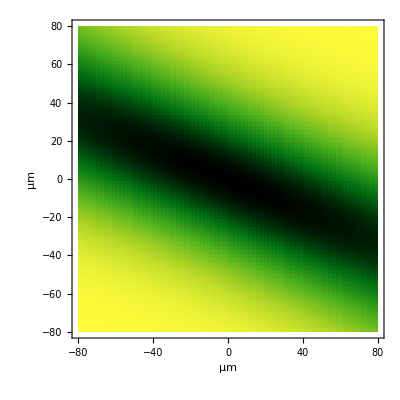

```mathematica
NicePlot[ odt[0.1,{x,y,0}],-100,100,80]
```

```mathematica
NicePlot[ir[6.,{x,y,0}]+odt[0.5,{x,y,0}],-100,100,80]
```

-Graphics-

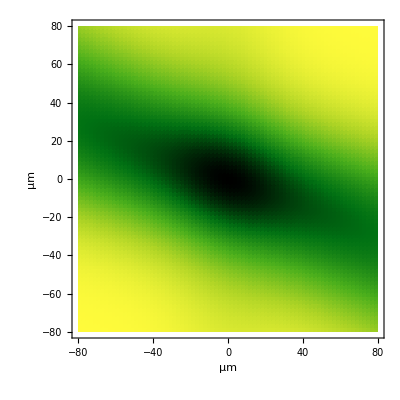

```mathematica
NicePlot[irLcr[6.,{x,y,0},1.]+odt[0.5,{x,y,0}],-100,100,80]
```

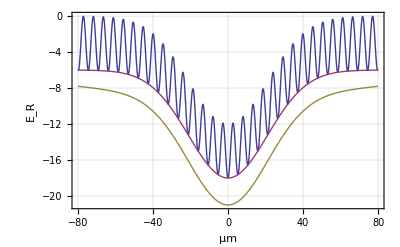

```mathematica
NicePlot1d[{comp[6.,0.,{x,0,0}],compBot[6.,0.,{x,0,0}],compOdtBot[6.,0.,0.05,{x,0,0}]},Automatic,80]
```

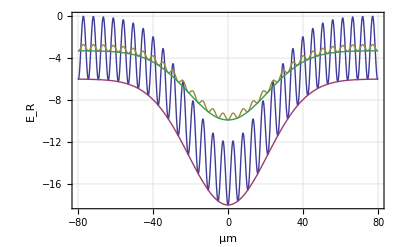

```mathematica
NicePlot1d[{compLcr[6.,0.,{x,0,0},0.],compLcrBot[6.,0.,{x,0,0},0.],compLcr[6.,0.,{x,0,0},99/100.],compLcrBot[6.,0.,{x,0,0},99/100.]},Automatic,80]
```

### Define lattice depth as a function of position and as a function of LCR rotation α. Lattice depth is a vector, for the depth along each direction.

```mathematica
v0pos[v0_,r_,α_]:= Module[ {v0x,v0y,v0z,λ=1.064,w0=42,R=1},
v0x=v0[[1]] √(R(1-α))( 1/(1+r[[1]]^2/((π w0^2/λ)^2)) Exp[-2(r[[2]]^2/w0^2+r[[3]]^2/w0^2)/(1+r[[1]]^2/((π w0^2/λ)^2))]);
v0y=v0[[2]] √(R(1-α))( 1/(1+r[[2]]^2/((π w0^2/λ)^2)) Exp[-2(r[[3]]^2/w0^2+r[[1]]^2/w0^2)/(1+r[[2]]^2/((π w0^2/λ)^2))]);
v0z=v0[[3]] √(R(1-α))( 1/(1+r[[3]]^2/((π w0^2/λ)^2)) Exp[-2(r[[1]]^2/w0^2+r[[2]]^2/w0^2)/(1+r[[3]]^2/((π w0^2/λ)^2))]);
{v0x,v0y,v0z}]
```

```mathematica
v0pos[{6,6,6},{10,0,0},0.1]
```

{5.69208,5.08198,5.08198}

### Get lattice depth at center for isotropic lattice, for a given rotation

```mathematica
v0[ErIR_,α_]:=v0pos[{ErIR,ErIR,ErIR},{0.,0.,0.},α][[1]]
```

### Define a function that plots lattice as a function of the distance along 111

```mathematica
latticeDiag[ErIR_,ErGR_,α_,x_]:=
Module[{r,scale=10},
r= {x/(√3),x/(√3),x/(√3)};
irLcrBot[ErIR,r,α]+gr[ErGR,r]+ v0pos[{ErIR,ErIR,ErIR},r,α] Cos[(2 π x)/(1.064 scale)]^2
]
```

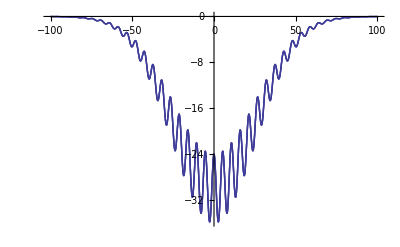
{5.257,-Graphics-}

```mathematica
Timing[Plot[latticeDiag[12.,0.,0.,x],{x,-100,100}]]
```

## Define function that gives band structure as a function of lattice depth vector

```mathematica
Clear[H];H[NPoints_,q_,V0_] := SparseArray[{{i_,i_}:>((q+2(i-1-NPoints))^2+V0/2), {i_,j_} /; i-j == 1 :>(V0/4),{i_,j_} /; i-j == -1:> (V0/4)},{2NPoints+1,2NPoints+1}] 
eigenval[NPoints_,q_,V0_,Band_]:=Sort[Eigenvalues[ H[NPoints,q,V0]]][[Band+1]]
eigenval3d[q_,v0_,Band_]:=Module[{NPoints,order,x,y,z, evals,bb,i,j,k},
NPoints=5; (*# of plane waves in each Bloch wave*)
order=Ordering[v0];
evals={Sort[Eigenvalues[ H[NPoints,q[[1]],v0[[1]]]]],Sort[Eigenvalues[ H[NPoints,q[[2]],v0[[2]]]]],Sort[Eigenvalues[ H[NPoints,q[[3]],v0[[3]]]]]};
bb=Band;i=1;j=1;k=1;
While[bb>0, i++; bb--;  If[bb>0,j++;bb--,None]; If[bb>0,k++;bb--,None]];
(*Print[i];
Print[j];
Print[k];
Print[evals];*)
evals[[order[[1]]]][[i]]+evals[[order[[2]]]][[j]]+evals[[order[[3]]]][[k]]
]
```

```mathematica
Flatten[Table[{{x,y},LCM[x,y]},{x,4},{y,4}],1]
```

### Speed up the evaluation of the above function by creating an interpolation table as a function of distance along the 111 direction

### BOTTOM OF FIRST BAND ALONG 111

#### Creation of table for the first time

```mathematica
bot0=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],0]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2]
fbot0=Interpolation[bot0]
Timing[GraphicsGrid[{{ContourPlot[fbot0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot0[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}]}}]]
```

{{{0.5,0.,0.},0.726602},{{0.5,0.,5.},0.713429},{{0.5,0.,10.},0.67528},{{0.5,0.,15.},0.616045},{{0.5,0.,20.},0.541521},{{0.5,0.,25.},0.458516},«6809»,{{19.5,1.,130.},0.},{{19.5,1.,135.},0.},{{19.5,1.,140.},0.},{{19.5,1.,145.},0.},{{19.5,1.,150.},0.}}

#### Reevaluation of table for subsequent uses

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

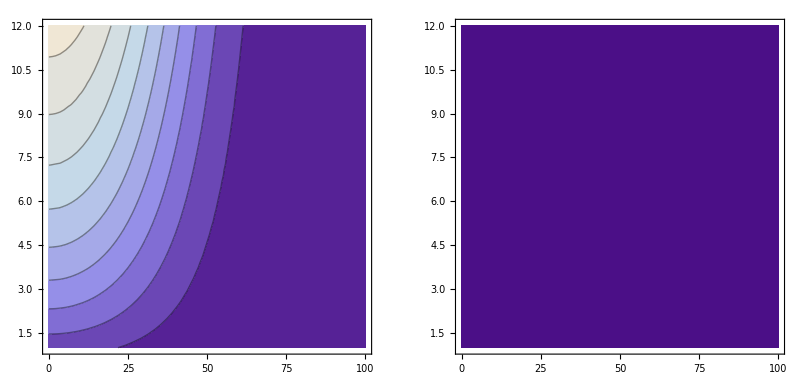
{0.14,-Graphics-}

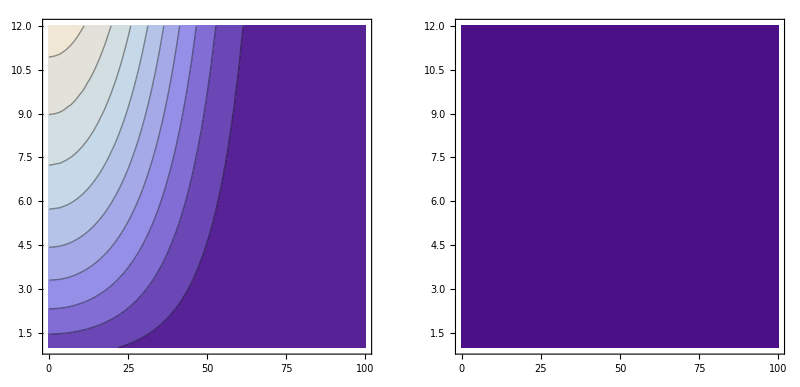
{13.058,-Graphics-}

```mathematica
bot0dat={{}, {{{{0.5,0.,0.},0.7266024109242162},{{0.5,0.,5.},0.7134292723429629},{{0.5,0.,10.},0.6752796822152769},{{0.5,0.,15.},0.6160445819063254},{{0.5,0.,20.},0.5415207785407423},{{0.5,0.,25.},0.45851574300105},«6809»,{{19.5,1.,130.},0.},{{19.5,1.,135.},0.},{{19.5,1.,140.},0.},{{19.5,1.,145.},0.},{{19.5,1.,150.},0.}}}, {}};
fbot0=Interpolation[bot0dat]
Timing[GraphicsGrid[{{ContourPlot[fbot0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot0[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}]}}]]
```

### TOP OF FIRST BAND ALONG 111

#### Creation of table for the first time

{{{0.5,0.,0.},3.36923},{{0.5,0.,5.},3.36242},{{0.5,0.,10.},3.34273},{{0.5,0.,15.},3.31224},{{0.5,0.,20.},3.27399},«6810»,{{19.5,1.,130.},3.},{{19.5,1.,135.},3.},{{19.5,1.,140.},3.},{{19.5,1.,145.},3.},{{19.5,1.,150.},3.}}

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

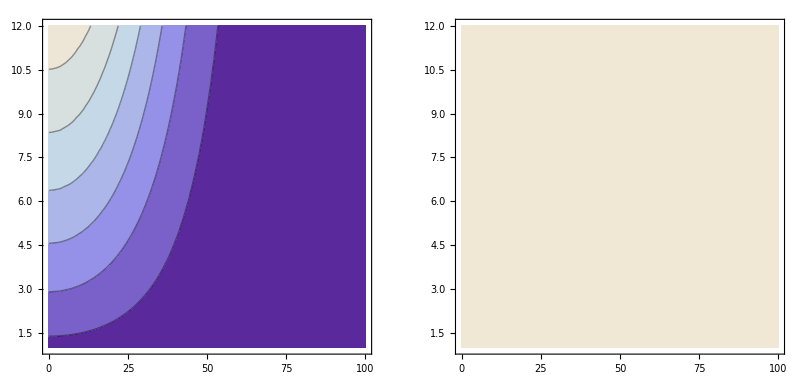
{0.093,-Graphics-}

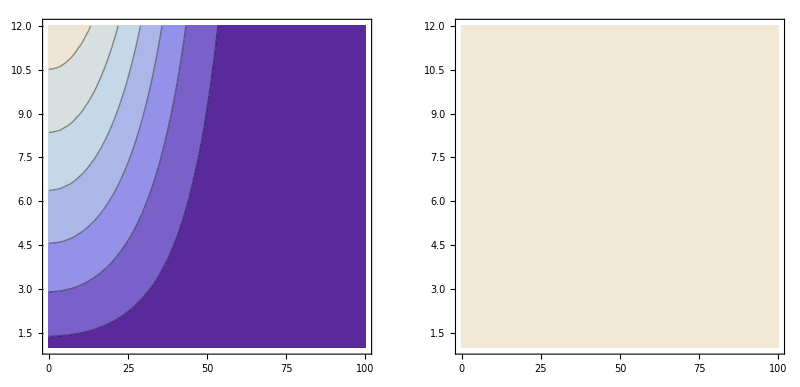
{10.062,-Graphics-}

```mathematica
top0=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],0]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2]
ftop0=Interpolation[top0]
Timing[GraphicsGrid[{{ContourPlot[ftop0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop0[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}]}}]]
```

#### Reevaluation of table for subsequent uses

```mathematica
top0dat={{}, {{{{0.5,0.,0.},3.369231674520395},{{0.5,0.,5.},3.36242423297106},{{0.5,0.,10.},3.342734986479324},{{0.5,0.,15.},3.312236828879178},{{0.5,0.,20.},3.2739918752883046},«6810»,{{19.5,1.,130.},3.},{{19.5,1.,135.},3.},{{19.5,1.,140.},3.},{{19.5,1.,145.},3.},{{19.5,1.,150.},3.}}}, {}};
ftop0=Interpolation[top0dat]
Timing[GraphicsGrid[{{ContourPlot[ftop0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop0[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}]}}]]
```

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

{0.093,-Graphics-}

{10.171,-Graphics-}

### BOTTOM OF SECOND BAND ALONG 111

#### Creation of table for the first time

{{{0.5,0.,0.},1.85742},{{0.5,0.,5.},1.84169},{{0.5,0.,10.},1.79618},{{0.5,0.,15.},1.72564},{{0.5,0.,20.},1.63709},{{0.5,0.,25.},1.53872},«6809»,{{19.5,1.,130.},1.},{{19.5,1.,135.},1.},{{19.5,1.,140.},1.},{{19.5,1.,145.},1.},{{19.5,1.,150.},1.}}

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

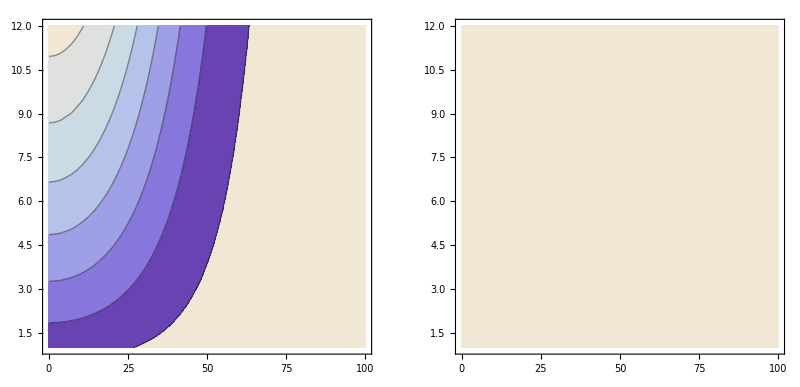
{0.109,-Graphics-}

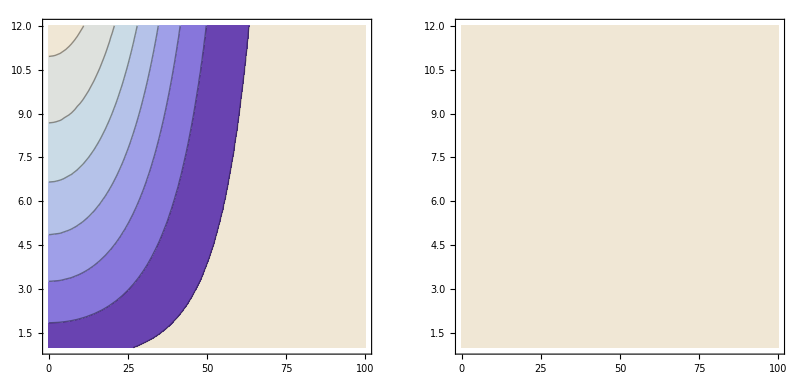
{11.138,-Graphics-}

```mathematica
bot1=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],1]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2]
fbot1=Interpolation[bot1]
Timing[GraphicsGrid[{{ContourPlot[fbot1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot1[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}]}}]]
```

#### Reevaluation of table for subsequent uses

```mathematica
bot1dat={{}, {{{{0.5,0.,0.},1.8574178151847685},{{0.5,0.,5.},1.8416901066622218},{{0.5,0.,10.},1.7961825933535032},{{0.5,0.,15.},1.7256400677509065},{{0.5,0.,20.},1.63709030631867},{{0.5,0.,25.},1.5387209335925698},«6809»,{{19.5,1.,130.},1.},{{19.5,1.,135.},1.},{{19.5,1.,140.},1.},{{19.5,1.,145.},1.},{{19.5,1.,150.},1.}}}, {}};
fbot1=Interpolation[bot1dat]
Timing[GraphicsGrid[{{ContourPlot[fbot1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot1[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}]}}]]
```

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

{0.109,-Graphics-}

{11.123,-Graphics-}

### TOP OF SECOND BAND ALONG 111

#### Creation of table for the first time

{{{0.5,0.,0.},4.7331},{{0.5,0.,5.},4.71969},{{0.5,0.,10.},4.68087},{{0.5,0.,15.},4.62067},{{0.5,0.,20.},4.54507},«6810»,{{19.5,1.,130.},4.},{{19.5,1.,135.},4.},{{19.5,1.,140.},4.},{{19.5,1.,145.},4.},{{19.5,1.,150.},4.}}

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

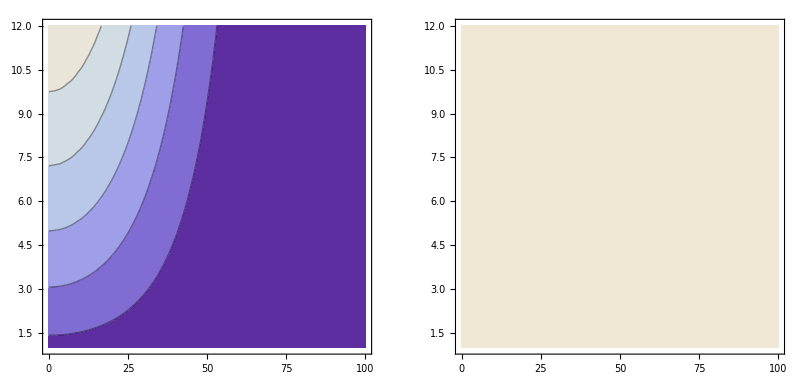
{0.093,-Graphics-}

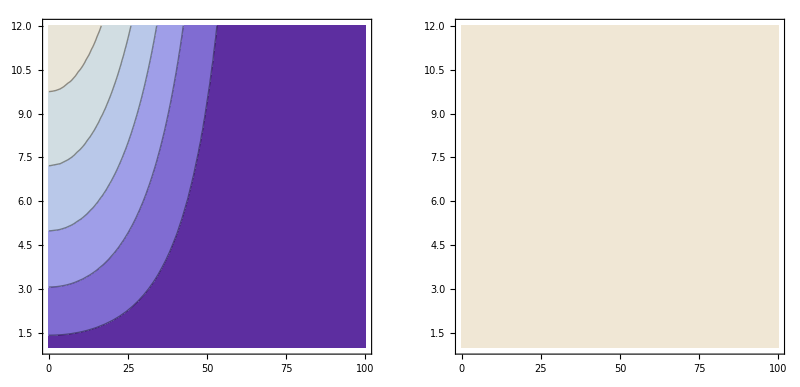
{9.547,-Graphics-}

```mathematica
top1=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],1]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2]
ftop1=Interpolation[top1]
Timing[GraphicsGrid[{{ContourPlot[ftop1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop1[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}]}}]]
```

#### Reevaluation of table for subsequent uses

```mathematica
top1dat={{}, {{{{0.5,0.,0.},4.733099612238808},{{0.5,0.,5.},4.719685974240609},{{0.5,0.,10.},4.680866903721065},{{0.5,0.,15.},4.620671151398881},{{0.5,0.,20.},4.545073091910393},«6810»,{{19.5,1.,130.},4.},{{19.5,1.,135.},4.},{{19.5,1.,140.},4.},{{19.5,1.,145.},4.},{{19.5,1.,150.},4.}}}, {}};
ftop1=Interpolation[top1dat]
Timing[GraphicsGrid[{{ContourPlot[ftop1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop1[ErIR,1.,x],{x,0,100},{ErIR,1,12}]}}]]
Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}]}}]]
```

InterpolatingFunction[{{0.5,19.5},{0.,1.},{0.,150.}},<>]

{0.093,-Graphics-}

{9.454,-Graphics-}

### Define functions that give bottom and top of band as a function of position. The three lattice beams are assumed to have the same depth v0 at r={0,0,0}.

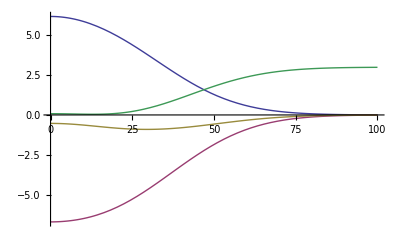
{0.592,-Graphics-}

```mathematica
bandBot[ErIR_,ErGR_,α_,x_]:=fbot0[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
bandTop[ErIR_,ErGR_,α_,x_]:=ftop0[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
band1Bot[ErIR_,ErGR_,α_,x_]:=fbot1[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
band1Top[ErIR_,ErGR_,α_,x_]:=ftop1[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
(*gravity[x_]:=1/(√3)x (0.00505)*)
Timing[Plot[{ fbot0[6.,0.,x],compLcrBot[6.,3.75,1/(√3){x,x,x},0.],bandBot[6.,3.75,0.,x],bandTop[6.,3.75,0.,x]},{x,0,100},PlotRange->All]]
```

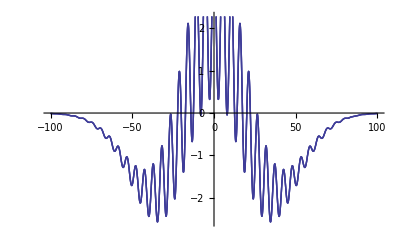

```mathematica
Plot[latticeDiag[12.,8.,0.9,x],{x,-100,100}]
```

### Define function to make a nice plot of the band for a given IR, GR, and ALPHA

```mathematica
band[ErIR_,ErGR_,α_]:=Module[{x},
Plot[{bandBot[ErIR,ErGR,α,x] ,bandTop[ErIR,ErGR,α,x],band1Bot[ErIR,ErGR,α,x] ,band1Top[ErIR,ErGR,α,x],latticeDiag[ErIR,ErGR,α,x]},{x,-100,100},Filling->{1->{2},3->{4}},GridLines->Automatic,Frame->True,FrameLabel->{"μm along (111)","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]
]
```

### Define function to make a nice plot of the band for a given IR, GR, and ODT

```mathematica
x
```

9

```mathematica
PadLeft["IR=",4," "]
```

PadLeft::normal: Nonatomic expression expected at position 1 in PadLeft["IR=", 4, " "].

PadLeft[IR=,4, ]

```mathematica
x=9.98;
y=10;
PadLeft[Characters["IR="],4," "]<>PadLeft[Characters[ToString[x]],5," "]<>"\nGR="<>PadLeft[Characters[ToString[y]],5," "]<>"\nα="
```

IR= 9.98
GR=   10
α=

```mathematica
band[ErIR_,ErGR_,α_]:=Module[{x},
Plot[{bandBot[ErIR,ErGR,α,√3 x 0.532] ,bandTop[ErIR,ErGR,α,√3 x 0.532],band1Bot[ErIR,ErGR,α,√3 x 0.532] ,band1Top[ErIR,ErGR,α,√3 x 0.532],latticeDiag[ErIR,ErGR,α,√3 x 0.532]},{x,-100,100},Filling->{1->{2},3->{4}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{380},AspectRatio-> 1.2,PlotRange->{-10,5},Epilog->Text[StandardForm[PadLeft[Characters["IR="],6," "]<>PadLeft[Characters[ToString[NumberForm[ErIR,{4,3}]]],6," "]<>"\n"<>PadLeft[Characters["GR="],6," "]<>PadLeft[Characters[ToString[NumberForm[ErGR,{4,3}]]],6," "]<>"\n"<>PadLeft[Characters["α="],6," "]<>PadLeft[Characters[ToString[NumberForm[α,{4,3}]]],6," "]],{50,-8.5}]]
]
```

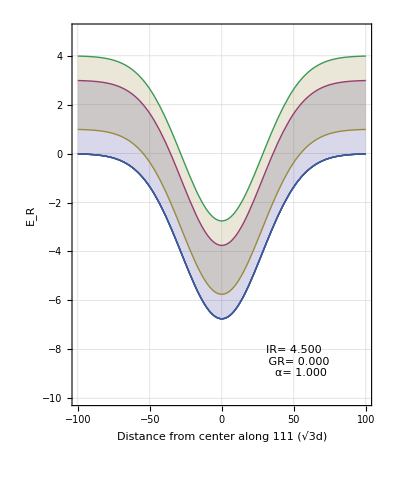

```mathematica
band[4.5,0,1.]
```

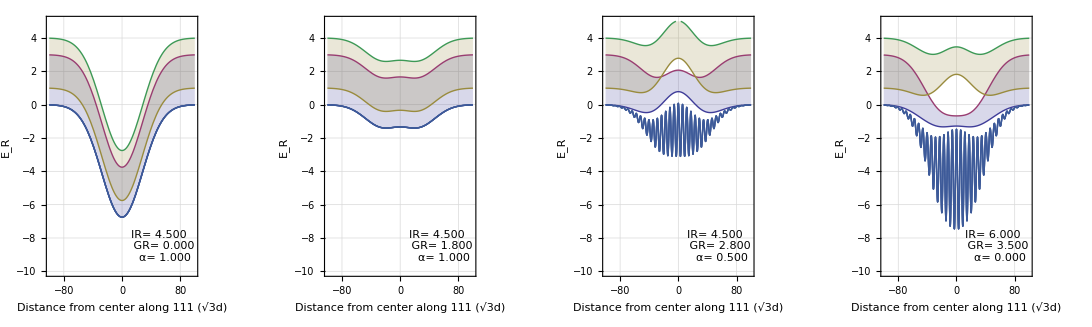

```mathematica
GraphicsGrid[{{band[4.5,0,1.],band[4.5,1.8,1.],band[4.5,2.8,0.5],band[6.,3.5,0.]}}]
```

### Optimize shape of band bottom to go from ALPHA=1 (dimple) to ALPHA=0 (lattice)

```mathematica
optTrap[α_]:=Module[{IR,GR,x},
desired=Table[ {x,bandBot[6.,3.5,0.,√3 x 0.532]},{x,0,100,1}];
trial=bandBot[IR,GR,α,√3 x 0.532];
fit=FindFit[desired,trial,{{IR,4.5},{GR,1.8}},x];
{IR,GR}/.fit
]
```

```mathematica
optimal=Table[{α,optTrap[α]},{α,0,1,0.05}]
```

{{0.,{6.,3.5}},{0.05,{5.91987,3.39904}},{0.1,{5.83903,3.29892}},{0.15,{5.7576,3.19982}},{0.2,{5.67577,3.10194}},{0.25,{5.59394,3.00556}},{0.3,{5.51215,2.91079}},{0.35,{5.43081,2.81785}},{0.4,{5.34981,2.72678}},{0.45,{5.26973,2.63783}},{0.5,{5.19023,2.55096}},{0.55,{5.1121,2.4664}},{0.6,{5.03455,2.38398}},{0.65,{4.95904,2.30404}},{0.7,{4.88363,2.2262}},{0.75,{4.81214,2.15107}},{0.8,{4.73809,2.07773}},{0.85,{4.70809,2.01032}},{0.9,{4.59843,1.93851}},{0.95,{4.3835,1.86823}},{1.,{4.4648,1.80826}}}

```mathematica
sequence=Table[{band[optimal[[i]][[2]][[1]],optimal[[i]][[2]][[2]],optimal[[i]][[1]]]},{i,1,Length[optimal],1}];
```

```mathematica
ListAnimate[Reverse[Flatten[sequence]]]
```

```mathematica
optIRf=InterpolatingPolynomial[{{-1,4},{0,2},{1,6}},a]
```

4+(1+a) (-2+3 a)

### Express optimal IR, GR, and α as a function of lattice depth

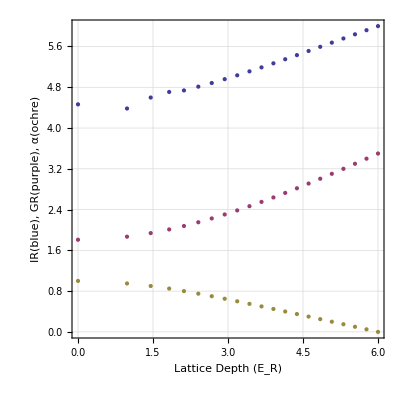

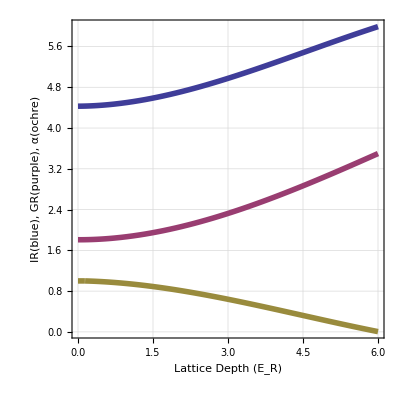

```mathematica
optIR=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[2]][[1]]},{i,1,Length[optimal],1}];
optGR=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[2]][[2]]},{i,1,Length[optimal],1}];
optAL=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[1]]},{i,1,Length[optimal],1}];

Clear[optIRf,optGRf,x];
optIRf=Fit[optIR,{1,x,x^2,x^3},x];
optGRf=Fit[optGR,{1,x,x^2,x^3},x];
optALf=Fit[optAL,{1,x,x^2,x^3},x];

optIRfun[v0_]:=optIRf/.{x->v0}
optGRfun[v0_]:=optGRf/.{x->v0}
optALfun[v0_]:=Max[Min[1.0,optALf/.{x->v0}],0.]

ListPlot[{optIR,optGR,optAL},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Lattice Depth (E_R)","IR(blue), GR(purple), α(ochre)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio-> 1.,PlotRange->{0,6}]

Plot[{optIRfun[x],optGRfun[x],optALfun[x]},{x,0.,6.},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Lattice Depth (E_R)","IR(blue), GR(purple), α(ochre)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio-> 1.,PlotRange->{0,6},PlotStyle->{Thickness[0.01]}]
```

### Define the lattice depth ramp-up curve, and from it derive the curves for IR, GR, and ALPHA

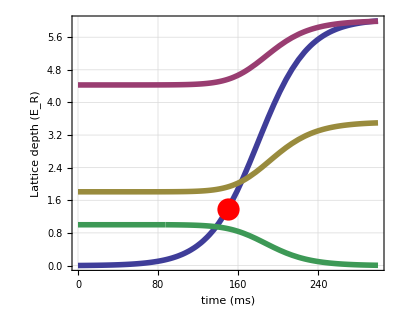

```mathematica
tanhRise[x_]:=Module[{
v0=0,
vf=6,
dt=300,
tau=50,
shift=180},
v0+(vf-v0)(1+Tanh[(x-shift)/tau]-(1+Tanh[-shift/tau]))/(1+Tanh[(dt-shift)/tau]-(1+Tanh[-shift/tau]))]
Plot[{tanhRise[t],optIRfun[tanhRise[t]],optGRfun[tanhRise[t]],optALfun[tanhRise[t]]},{t,0.,300.},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"time (ms)","Lattice depth (E_R)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio->0.8,PlotRange->{0,6},PlotStyle->{Directive[Thickness[0.01],ColorData[1,1]],Directive[Thickness[0.01],ColorData[1,2]],Directive[Thickness[0.01],ColorData[1,3]],Directive[Thickness[0.01],ColorData[1,4]]},Epilog->{Red,PointSize[0.04],Point[{150.,tanhRise[150.]}]}]
```

### Plot full movie as a function of time

```mathematica
fullout[time_]:=
GraphicsGrid[{{band[optIRfun[tanhRise[time]],optGRfun[tanhRise[time]],optALfun[tanhRise[time]] ],Plot[{tanhRise[t],optIRfun[tanhRise[t]],optGRfun[tanhRise[t]],optALfun[tanhRise[t]]},{t,0.,300.},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"time (ms)","Lattice depth (E_R)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio->0.8,PlotRange->{0,6},PlotStyle->{Directive[Thickness[0.01],ColorData[1,1]],Directive[Thickness[0.01],ColorData[1,2]],Directive[Thickness[0.01],ColorData[1,3]],Directive[Thickness[0.01],ColorData[1,4]]},Epilog->{Red,PointSize[0.04],Point[{time,tanhRise[time]}]}]}}
]
```

```mathematica
sequence=Table[fullout[time],{time,0.,300.,25.}];
```

```mathematica
ListAnimate[sequence]
```

## Older stuff

### Define function to make plot of dimple

```mathematica
dimplePlot[ErIR_,ErGR_,fcpow_,ErIRd_,ErGRd_,fcpowd_]:=Module[{coord,x},
coord=0.532{x,x,x};
Plot[{bandBot[ErIR,ErGR,fcpow,coord] ,bandTop[ErIR,ErGR,fcpow,coord],band1Bot[ErIR,ErGR,fcpow,coord] ,band1Top[ErIR,ErGR,fcpow,coord],latticeDiag[ErIR,ErGR,fcpow,√3 x 0.532],compDimple[ErIRd,ErGRd,fcpowd,coord] },{x,-100,100},Filling->{1->{2},3->{4}},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Thickness[0.015],ColorData[1,1]]},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400},AspectRatio-> 1.2,PlotRange->{-10,5}]
]
```

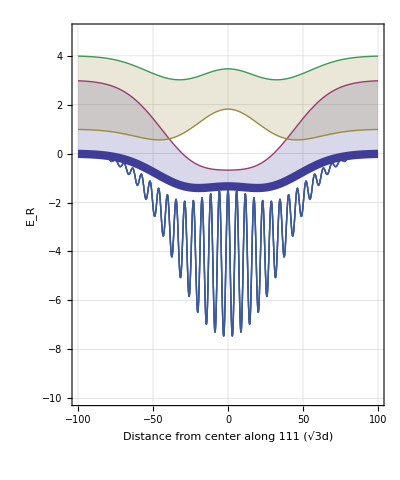

```mathematica
d0=dimplePlot[6.,3.5,0.,   4.5,1.8,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_4p5IR_1p8GR.png",d0,ImageResolution->240]
```

6IR_3p5GR+dimple_4p5IR_1p8GR.png

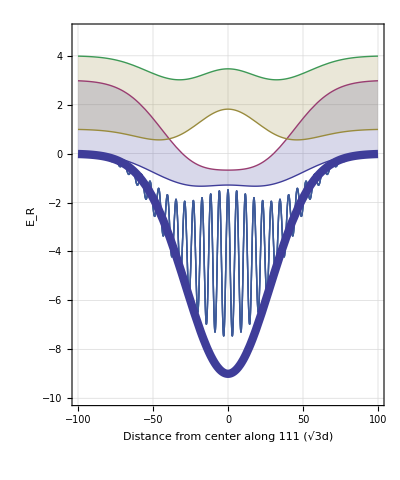

```mathematica
d1=dimplePlot[6.,3.5,0.,   6,0,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_6IR_0GR.png",d1,ImageResolution->240]
```

6IR_3p5GR+dimple_6IR_0GR.png

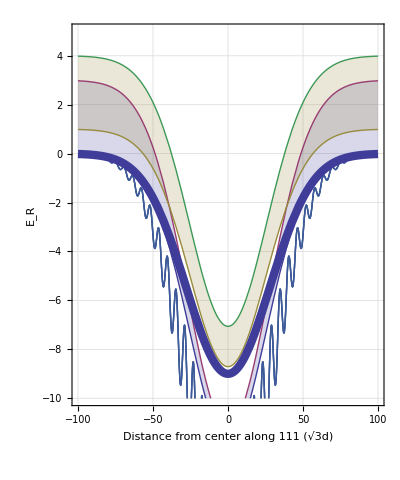

```mathematica
d2=dimplePlot[6.,0,0.,   6.,0,0.0]
```

```mathematica
Export["6IR_0GR+dimple_6IR_0R.png",d2,ImageResolution->240]
```

6IR_0GR+dimple_6IR_0R.png

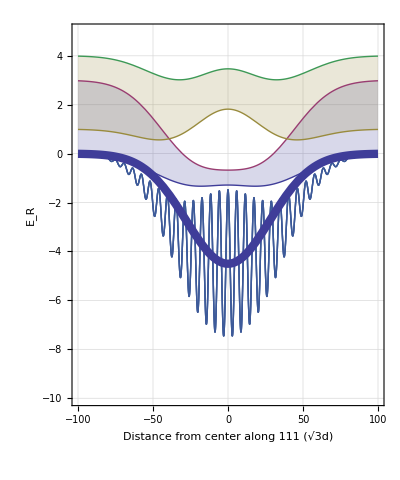

```mathematica
d3=dimplePlot[6.,3.5,0.,   3,0,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_3IR_0R.png",d3,ImageResolution->240]
```

6IR_3p5GR+dimple_3IR_0R.png

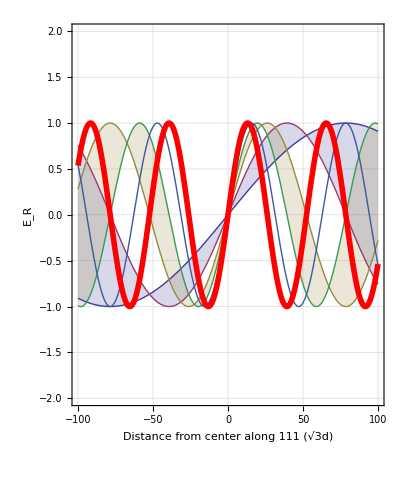

```mathematica
Plot[{Sin[x/50],Sin[2x/50],Sin[3x/50] ,Sin[4x/50],Sin[5x/50],Sin[6x/50] },{x,-100,100},Filling->{1->{2},3->{4}},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Thickness[0.01],Red]},GridLines->Automatic,Frame->True,FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400},AspectRatio-> 1.2,PlotRange->{-2,2}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\pedro\apparatus3\1108-antilattice\potentials

```mathematica
Export["compensated_10_6p8_0.05_two_bands.png",%%%]
```

compensated_10_6p8_0.05_two_bands.png

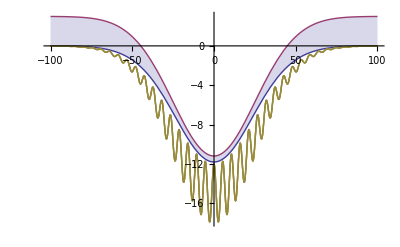

```mathematica
band[6.,0.,0.]
```

```mathematica
compensated[ErIR_]:=Table[band[ErIR,ErGR,0.0],{ErGR,{0.,0.33 ErIR,0.66 ErIR, ErIR}}]
```

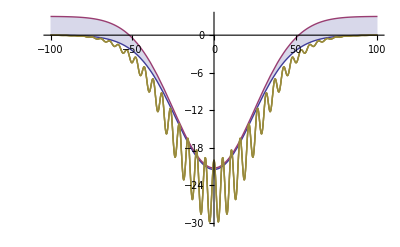
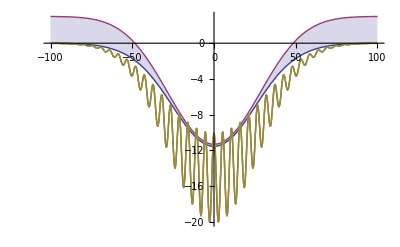
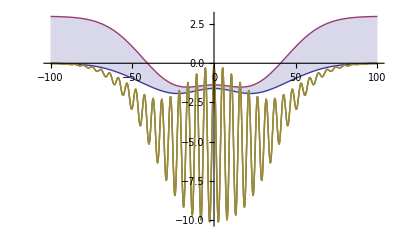
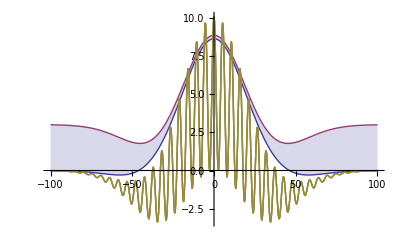

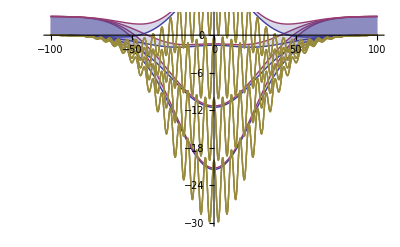

```mathematica
c10=compensated[10]
Show[c10]
```

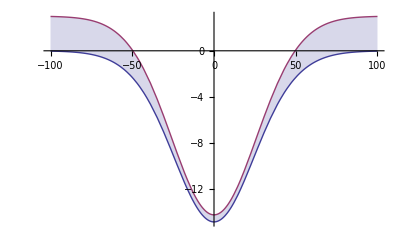
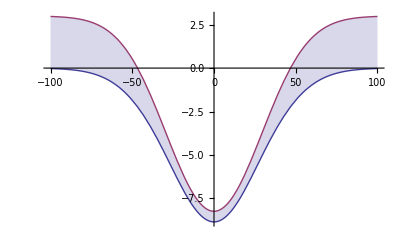
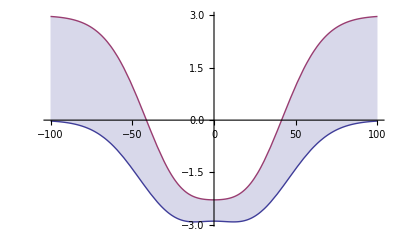
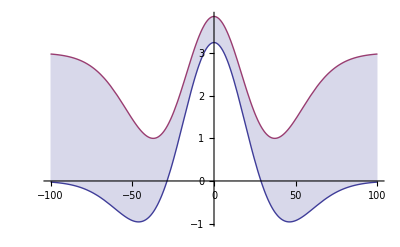

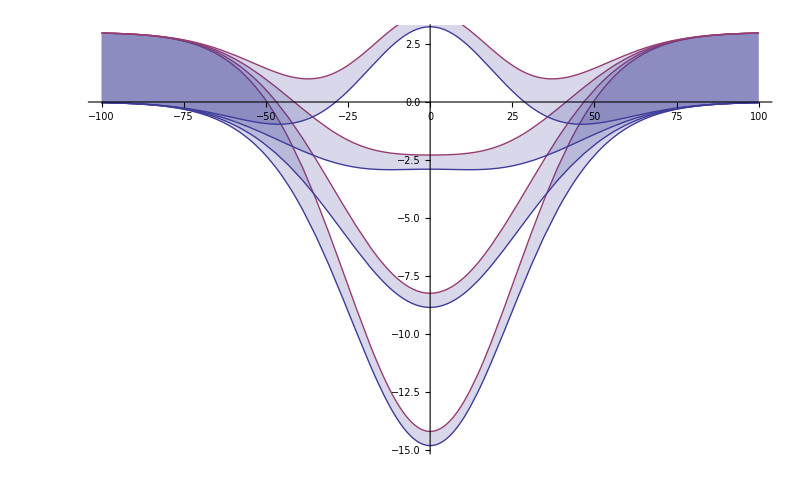

```mathematica
c6=compensated[6]
Show[c6]
```

### Gravity in units of recoil per micrometer

Mass of lithium is 9.96e-27 kg
Acceleration of gravity is 9.8 m/s^2 = 980 cm/s^2

mgh = Er = kb (1.4 uK)

kb/m = 13.85 cm^2 / s^2 / uK

so  h  =  ( 13.85 cm^2 / s^2 / uK ) ( 1.4 uK ) / g =  ( 19.39 / 980 ) cm =  1.979 e-2 cm = 197.9 um 

Therefore in recoils per micrometer the potential of gravity on a lihtium atom is 

gravity  = 5.05e-3 Er/um